```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/sebastian/Dropbox/ICHEP_Recasting/Sebastian/All_validations

```mathematica
fudge=1.5;limfix=1;
```

#### import limits for each search and SR

```mathematica
searches = {"ATLAS_1lepton_j_MET","ATLAS_ss_leptons","ATLAS_multib","ATLAS_7_10_jet_3fb","ATLAS_RPV","ATLAS_CONF2016078_2_6j","CMS_jets","ATLAS_lepton_multijet","ATLAS_8_10_jet"};
```

```mathematica
SRtags["ATLAS_1lepton_j_MET"]={"GG2J","GG6k bulk","GG6J high M","GG4j high x","GG4J low x","SS4J x=1/2","SS5j x=1/2","SS4J low x","SS5J high x"};
σ95lim["ATLAS_1lepton_j_MET"]={1.44,1.49,0.35,0.28,1000,0.37,0.51,0.43,0.59,0.49}10^-3 pb;
SRtags["ATLAS_multib"]={"Gbb-A","Gbb-B","Gtt-0L A","Gtt-0L B","Gtt-1L A","Gtt-1L B","Gtt-1L C"};
σ95lim["ATLAS_multib"]={0.31,0.68,0.25,0.90,0.26,0.33,0.38}10^-3 pb;
SRtags["ATLAS_RPV"]={"4jSRb1","4jSR","5jSRb1","5jSR"};
σ95lim["ATLAS_RPV"]={1.76,3.11,2.00,2.94}10^-3 pb;
SRtags["ATLAS_CONF2016078_2_6j"]={"2j800","2j1200","2j1600","2j2000","3j1200","4j1000","4j1400","4j1800","4j2200","4j2600","5j1400","6j1800","6j2200"};
σ95lim["ATLAS_CONF2016078_2_6j"]={11,3.7,1.4,0.73,6.0,2.6,1.9,1.7,0.89,0.38,1.6,0.83,0.27}10^-3 pb;
SRtags["ATLAS_7_10_jet_3fb"]={"8j50","8j50-1b","8j50-2b","9j50","9j50-1b","9j50-2b","10j50","10j50-1b","10j50-2b","7j80","7j80-1b","7j80-2b","8j80","8j80-1b","8j80-2b"};
σ95lim["ATLAS_7_10_jet_3fb"]={11,6.8,3.8,5.8,5,2.6,2.5,1.6,1.1,10,6.2,4.2,3.2,1.7,1.4}10^-3 pb;
SRtags["CMS_jets"]="SR"<>ToString[#]&/@Range[12];
N95["CMS_jets"]={282,13.2,69,7.3,4.3,30.3,28.6,9.2,5.2,3.0,41,12.1};σ95lim["CMS_jets"]=N95["CMS_jets"]/12.9 * 10^-3 pb;
SRtags["ATLAS_ss_leptons"]={"SR3L1", "SR3L2", "SR0b1", "SR0b2", "SR1b", "SR3b", "SR1bDD", "SR3bDD", "SR1bGG"};
σ95lim["ATLAS_ss_leptons"]={0.59,0.38,0.47,0.24,0.78,0.37,0.75,0.56,0.36}10^-3 pb;
SRtags["ATLAS_lepton_multijet"]={"n40_8_0","n40_8_3","n40_9_0","n40_9_3","n40_10_0","n40_10_3","n60_8_0","n60_8_3","n60_9_0","n60_9_3","n60_10_0","n60_10_3"};
σ95lim["ATLAS_lepton_multijet"]={2.2,8.4,1.1,2.8,0.43,1.19,1.2,1.5,0.97,0.5,0.2,0.26}10^-3 pb;
SRtags["ATLAS_8_10_jet"]={"8j50\nMJ340","9j50\nMJ340","10j50\nMJ340","8j50\nMJ500","9j50\nMJ500","10j50\nMJ500"};
σ95lim["ATLAS_8_10_jet"]={3.5,1.7,1.1,1.9,1.6,0.83}10^-3 pb;
```

```mathematica
σ95exp["ATLAS_1lepton_j_MET"]={20.2,14.7,5.5,5.2,10000,6.6,6.9,9.1,6.6,8.8}/14.8* 10^-3 pb;
σ95exp["ATLAS_multib"]={4.3,12,3.9,7.1,3.9,3.6,6.9}/14.8 * 10^-3 pb;
σ95exp["ATLAS_RPV"]={2.5,4.4,1.08,2.03}* 10^-3 pb;
σ95exp["ATLAS_CONF2016078_2_6j"]= {115,63,30,15.9,74,24,23,14,7.9,4.8,24,6.5,3.3}* 10^-3 pb;
σ95exp["ATLAS_7_10_jet_3fb"]= { 49,37,22,19,17,10,6,6,4,32,24,14,11,7,5}/3.2* 10^-3 pb;
σ95exp["ATLAS_ss_leptons"]= { 7.6,4.0,7.9,3.9,0.97,4.2,9.8,4.7,4.1}/13.2* 10^-3 pb;(*{ 7.6,4.0,7.9,3.9,0.97,4.2,4.1,9.8,4.7}/13.2* 10^-3 pb;*)
σ95exp["CMS_jets"]={193,10.6,51.5,8.1,3.0,24,17.4,6.3,3.0,3.0,74.5,10.5}/12.9 * 10^-3 pb;
σ95exp["ATLAS_lepton_multijet"]={3.3,4.7,1.1,2.1,0.52,1.1,1.1,1.4,0.46,0.6,0.2,0.29}* 10^-3 pb;
σ95exp["ATLAS_8_10_jet"]={82,35,19,41,27,12}/18.2* 10^-3 pb;
```

#### import official limit plots

```mathematica
LHCplotsDir=(*NotebookDirectory[]<>*)"official_figs/";
```

```mathematica
LHCplotsfiles=FileNames["*.dat",LHCplotsDir]
```

{official_figs/ATLAS_1L_fig06a.dat,official_figs/ATLAS_26j_fig09a.dat,official_figs/ATLAS_26j_fig09b.dat,official_figs/ATLAS_26j_fig10a.dat,official_figs/ATLAS_710_jets_a.dat,official_figs/ATLAS_710_jets_b.dat,official_figs/ATLAS_810_jets_a.dat,official_figs/ATLAS_810_jets_b.dat,official_figs/ATLAS_b_fig_07a.dat,official_figs/ATLAS_b_fig_08.dat,official_figs/ATLAS-lepton_multijet-fig6top.dat,official_figs/ATLAS_RPV_fig_05a.dat,official_figs/ATLAS_RPV_fig_05b.dat,official_figs/ATLAS-ss-fig6b.dat,official_figs/CMS_fig_09c.dat,official_figs/CMS_fig_10a.dat,official_figs/CMS_fig_10b.dat,official_figs/CMS_fig_10c.dat}

```mathematica
validationfile["ATLAS_1lepton_j_MET"]={"ATLAS_1L_fig06a.dat"};
validationfile["ATLAS_ss_leptons"]={"ATLAS-ss-fig6b.dat"};
validationfile["ATLAS_multib"]={"ATLAS_b_fig_07a.dat","ATLAS_b_fig_08.dat"};
validationfile["ATLAS_7_10_jet_3fb"]={"ATLAS_710_jets_a.dat","ATLAS_710_jets_b.dat"};
validationfile["ATLAS_RPV"]={"ATLAS_RPV_fig_05a.dat","ATLAS_RPV_fig_05b.dat"};
validationfile["ATLAS_CONF2016078_2_6j"]={"ATLAS_26j_fig09a.dat","ATLAS_26j_fig09b.dat","ATLAS_26j_fig10a.dat"};
validationfile["CMS_jets"]={"CMS_fig_09c.dat","CMS_fig_10a.dat","CMS_fig_10b.dat","CMS_fig_10c.dat"};
validationfile["ATLAS_lepton_multijet"]={"ATLAS-lepton_multijet-fig6top.dat"};
validationfile["ATLAS_8_10_jet"]={"ATLAS_810_jets_a.dat","ATLAS_810_jets_b.dat"};
```

```mathematica
For[ss=1,ss≤ Length[searches],ss++,
(*{Print[#],*)validationplots[searches[[ss]] ]=Import[LHCplotsDir<>#](*}*)&/@validationfile[searches[[ss]]];
]
```

```mathematica
validationdata["ATLAS_RPV",2]
```

validationdata[ATLAS_RPV,2]

```mathematica
validationplots["ATLAS_RPV"][[2]]
```

{{900.352,0.441},{920.968,0.387},{952.317,0.329},{987.467,0.289},{1038.51,0.229},{1078.18,0.194},{1122.44,0.162},{1161.48,0.134},{1196.78,0.118},{1247.97,0.095},{1296.11,0.081},{1329.57,0.073},{1379.98,0.064},{1413.37,0.059},{1460.1,0.054},{1507.33,0.049},{1537.05,0.045},{1580.12,0.041},{1622.33,0.038},{1661.65,0.036},{1691.44,0.034},{1738.32,0.032},{1771.77,0.03},{1798.31,0.029}}

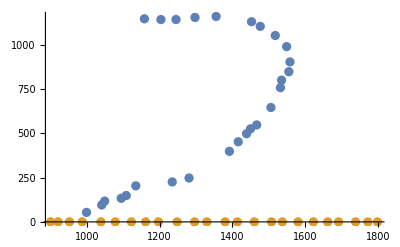

```mathematica
ListPlot[validationplots["ATLAS_RPV"]]
```

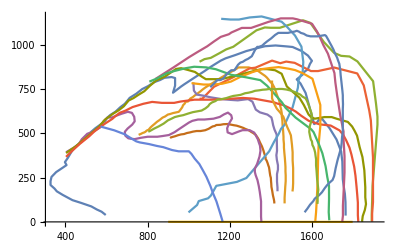

```mathematica
ListPlot[Flatten[validationplots/@searches,1],Joined->True]
```

#### import cross sections

```mathematica
massesgluinoNLO=Transpose[Import["gluino_xsec.dat"][[3;;]]][[2]];
crossgluinoNLOlist=Transpose[Import["gluino_xsec.dat"][[3;;]]][[5]];
crossxgluinoNLO[m_]=pb 10^(Interpolation[Outer[Log10,Transpose[{massesgluinoNLO,crossgluinoNLOlist}]],"ExtrapolationHandler"->{Indeterminate&,"WarningMessage"->False},InterpolationOrder->1][Log10[m]]);
massessquarkNLO=Transpose[Import["squark_xsec.dat"][[5;;]]][[2]];
crosssquarkNLOlist=Transpose[Import["squark_xsec.dat"][[5;;]]][[5]];
crossxsquarkNLO[m_]=pb 10^(Interpolation[Outer[Log10,Transpose[{massessquarkNLO,crosssquarkNLOlist}]],"ExtrapolationHandler"->{Indeterminate&,"WarningMessage"->False},InterpolationOrder->1][Log10[m]]);
```

#### Import all efficiencies

```mathematica
EffDir="efficiencies_slim/"
```

efficiencies_slim/

```mathematica
(*validgrids["ATLAS_1lepton_j_MET"]={"M3_C1_N1_results_fat_stable_lepton_results"};
validgrids["ATLAS_ss_leptons"]={"M3_tt_M1_results_fat_stable_lepton_results"};
validgrids["ATLAS_multib"]={"M3_bb_M1_results_fat_stable_lepton_results","M3_tt_M1_results_fat_stable_lepton_results"};
validgrids["ATLAS_7_10_jet_3fb"]={"M3_mu_M1_results_fat_stable_lepton_results"};
validgrids["ATLAS_RPV"]={"M3_M1_results_fat_stable_lepton_results","M3_line_results_RPV_fat_lepton_results"};
validgrids["ATLAS_CONF2016078_2_6j"]={"sq_M1_results_fat_stable_lepton_results","M3_M1_results_fat_stable_lepton_results","M3_C1_N1_results_fat_stable_lepton_results"};
validgrids["CMS_jets"]={"sq_M1_results_fat_stable_lepton_results","M3_tt_M1_results_fat_stable_lepton_results","M3_bb_M1_results_fat_stable_lepton_results","M3_M1_results_fat_stable_lepton_results"};
validgrids["ATLAS_lepton_multijet"]={"M3_tt_M1_results_RPV_fat_lepton_results"};
validgrids["ATLAS_8_10_jet"]={"M3_mu_M1_results_fat_stable_lepton_results"};*)
```

```mathematica
validgrids["ATLAS_1lepton_j_MET"]={"M3_C1_N1"};
validgrids["ATLAS_ss_leptons"]={"M3_tt_M1"};
validgrids["ATLAS_multib"]={"M3_bb_M1","M3_tt_M1"};
validgrids["ATLAS_7_10_jet_3fb"]={"M3_mu_M1","M3_C1_N2_N1"};
validgrids["ATLAS_RPV"]={"M3_M1","M3_line"};
validgrids["ATLAS_CONF2016078_2_6j"]={"squark_M1","M3_M1","M3_C1_N1"};
validgrids["CMS_jets"]={"squark_M1","M3_tt_M1","M3_bb_M1","M3_M1"};
validgrids["ATLAS_lepton_multijet"]={"M3_tt_M1"};
validgrids["ATLAS_8_10_jet"]={"M3_mu_M1","M3_C1_N2_N1"};
```

```mathematica
For[ss=1,ss≤ Length[searches],ss++,
(*{Print[searches[[ss]]<>"."<>#<>".dat"],*)validationdata[searches[[ss]] ]=Import[EffDir<>searches[[ss]]<>"."<>#<>".dat"](*}*)&/@(validgrids[searches[[ss]]])
]
```

```mathematica
validgrids["ATLAS_8_10_jet"]
```

{M3_mu_M1,M3_C1_N2_N1}

```mathematica
crossxsquarkNLO[massesgrid["ATLAS_RPV",2][[1]]]
```

0.0313372 pb

```mathematica
(*For[ss=1,ss≤ Length[searches],ss++,
For[vv=1,vv≤ Length[validgrids[searches[[ss]]]],vv++,
If[validgrids[searches[[ss]]][[vv]]≠  "M3_C1_N1_results_fat_stable_lepton_results",massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[{2,4}]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];
If[validgrids[searches[[ss]]][[vv]]=="M3_line_results_RPV_fat_lepton_results",massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[2]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];],massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[{2,6}]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];];
efficiencies[searches[[ss]],vv]=validationdata[searches[[ss]]][[vv]][[2;;;;2]];
For[ii=1,ii≤  Length[massesgrid[searches[[ss]],vv]],ii++,
mm=massesgrid[searches[[ss]],vv][[ii]];
(*MaxSRexp02b[mm]=Position[(crossxgluinoNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]]),Max[(crossxgluinoNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]])]];*)
Eps[searches[[ss]],vv][mm]=efficiencies[searches[[ss]],vv][[ii]][[2;;]];
]
]
]*)
```

```mathematica
(*For[ss=1,ss≤ Length[searches],ss++,
For[vv=1,vv≤ Length[validgrids[searches[[ss]]]],vv++,
If[validgrids[searches[[ss]]][[vv]]≠  "M3_C1_N1_results_fat_stable_lepton_results",massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[{2,4}]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];

If[validgrids[searches[[ss]]][[vv]]=="M3_line_results_RPV_fat_lepton_results",massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[2]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];]

If[validgrids[searches[[ss]]][[vv]]=="M3_line_results_RPV_fat_lepton_results",massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[2]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];],massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[{2,6}]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];];
efficiencies[searches[[ss]],vv]=validationdata[searches[[ss]]][[vv]][[2;;;;2]];
For[ii=1,ii≤  Length[massesgrid[searches[[ss]],vv]],ii++,
mm=massesgrid[searches[[ss]],vv][[ii]];

If[validgrids[searches[[ss]]][[vv]]≠  "M3_line_results_RPV_fat_lepton_results",MaxSRexp[searches[[ss]],vv][mm]=Position[(crossxgluinoNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]]),Max[(crossxgluinoNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]])]];
If[validgrids[searches[[ss]]][[vv]]=="sq_M1_results_fat_stable_lepton_results",MaxSRexp[searches[[ss]],vv][mm]=Position[(crossxsquarkNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]]),Max[(crossxsquarkNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]])]];],


MaxSRexp[searches[[ss]],vv][mm]=Position[(crossxsquarkNLO[mm]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]]),Max[(crossxsquarkNLO[mm]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]])]];];

Eps[searches[[ss]],vv][mm]=efficiencies[searches[[ss]],vv][[ii]][[2;;]];
]
]
]*)
```

#### Define plot-making functions - Best observed

```mathematica
For[ss=1,ss≤ Length[searches],ss++,
For[vv=1,vv≤ Length[validgrids[searches[[ss]]]],vv++,
If[validgrids[searches[[ss]]][[vv]]≠  "M3_C1_N1",massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[{2,4}]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];

If[validgrids[searches[[ss]]][[vv]]=="M3_C1_N2_N1",massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[{2,8}]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];]

If[validgrids[searches[[ss]]][[vv]]=="M3_line",massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[2]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];],massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[{2,6}]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];];
efficiencies[searches[[ss]],vv]=validationdata[searches[[ss]]][[vv]][[2;;;;2]];
For[ii=1,ii≤  Length[massesgrid[searches[[ss]],vv]],ii++,
mm=massesgrid[searches[[ss]],vv][[ii]];

If[validgrids[searches[[ss]]][[vv]]≠  "M3_line",MaxSRObs[searches[[ss]],vv][mm]=Position[(crossxgluinoNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95lim[searches[[ss]]]),Max[(crossxgluinoNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95lim[searches[[ss]]])]];
If[validgrids[searches[[ss]]][[vv]]=="squark_M1",MaxSRObs[searches[[ss]],vv][mm]=Position[(crossxsquarkNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95lim[searches[[ss]]]),Max[(crossxsquarkNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95lim[searches[[ss]]])]];],


MaxSRObs[searches[[ss]],vv][mm]=Position[(crossxsquarkNLO[mm]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95lim[searches[[ss]]]),Max[(crossxsquarkNLO[mm]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95lim[searches[[ss]]])]];];


]
]
]
```

```mathematica
MaxSRexp["ATLAS_RPV",1][{#[[1]],#[[2]]}]&/@massesgrid["ATLAS_RPV",1]
```

{{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}}}

```mathematica
MaxSRObs["ATLAS_RPV",1][{#[[1]],#[[2]]}]&/@massesgrid["ATLAS_RPV",1]
```

{{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{2}},{{4}},{{2}},{{2}},{{2}},{{2}}}

```mathematica
limitsSR[m1_,m2_,search_,grid_,n_]:=((crossxgluinoNLO[m1]Eps[search,grid][{m1,m2}])/σ95lim[search])[[n]]
limitsobs[m1_,m2_,search_,grid_]:=Max[limitsSR[m1,m2,search,grid,#]&/@Range[Length[σ95lim[search]]]]
bestlim[m1_,m2_,search_,grid_]:= SRtags[[Ordering[Table[limitsSR[m1,m2,search,grid,n],{n,1,Length[SRtags[search]]}]][[-1]]]]
limitsSR[m1_,m2_,"ATLAS_CONF2016078_2_6j",1,n_]:=((crossxsquarkNLO[m1]Eps["ATLAS_CONF2016078_2_6j",1][{m1,m2}])/σ95lim["ATLAS_CONF2016078_2_6j"])[[n]]
limitsSR[m1_,m2_,"CMS_jets",1,n_]:=((crossxsquarkNLO[m1]Eps["CMS_jets",1][{m1,m2}])/σ95lim["CMS_jets"])[[n]]
```

```mathematica
makeLHCplot[search_,val_]:=ListPlot[validationplots[search][[val]],Joined-> True,PlotStyle->Red]
makeExclusionsPlotobs[search_,val_]:=
(If[validgrids[search][[val]]=="M3_tt_M1",epi={{Dashed,Line[degline["M3_M1"]]},{Dashed,Line[degline["M3_tt_M1"]]}},epi={Dashed,Line[degline[validgrids[search][[val]]]]}];
ListContourPlot[{#1,#2,limitsobs[#1,#2,search,val]}&@@@massesgrid[search,val],Contours->{1/fudge,1,fudge},ContourShading->{None,Opacity[0.15,Blue],Opacity[0.15,Blue],None},ContourStyle->{None,{Thick,Blue},None},Epilog-> {epi,Text[label[search][[1]],Scaled[{0.78,0.95}]],Text[label[search][[2]],Scaled[{0.78,0.88}]]}])
makePlotobs[search_,val_,options___]:=Show[makeExclusionsPlotobs[search,val],makeLHCplot[search,val],AspectRatio->1/GoldenRatio,Frame-> True,FrameLabel-> framelabel[search,val],FrameStyle-> 13,options]
```

```mathematica
σsimobs=Table[{m,Min[1/pb σ95lim["ATLAS_RPV"][[#]]/ Eps["ATLAS_RPV",2][m][[#]]&/@Range[Length[σ95lim["ATLAS_RPV"]]]]},{m,(Sort@massesgrid["ATLAS_RPV",2])}]//Quiet;
makeLHCplot["ATLAS_RPV",2]=ListLogPlot[validationplots["ATLAS_RPV"][[2]],Joined->True, PlotStyle->{{Thick,Red}}];
makeExclusionsPlotobs["ATLAS_RPV",2]:=Show[ListLogPlot[{{#1,1/fudge#2}&@@@σsimobs,σsimobs,{#1,fudge#2}&@@@σsimobs},Joined->True, PlotStyle->{None,Blue,None},Filling->{1->{ 3}},Epilog-> {Text[label["ATLAS_RPV"][[1]],Scaled[{0.78,0.95}]],Text[label["ATLAS_RPV"][[2]],Scaled[{0.78,0.88}]]}],LogPlot[crossxgluinoNLO[m]/pb,{m,500,2000},PlotStyle->Black]]
```

#### Define plot-making functions -Best expected

```mathematica
massesgrid["ATLAS_7_10_jet_3fb",2][[1]]
```

{1000,525}

```mathematica
limits[1000,525,"ATLAS_7_10_jet_3fb",2]
```

8.51215

```mathematica
massesgrid["ATLAS_1lepton_j_MET",1]
```

{{1100,1050},{1100,50},{1100,250},{1100,450},{1100,650},{1100,850},{1300,850},{1300,1050},{1300,50},{1300,250},{1300,650},{1500,650},{1500,850},{1500,1050},{1300,450},{1500,50},{1500,250},{1500,450},{1700,450},{1700,650},{1700,1050},{1700,850},{1700,250},{1700,50},{1900,450},{1900,650},{1900,250},{1900,1050},{1900,50},{2100,650},{500,50},{2100,50},{2100,450},{2100,1050},{1900,850},{2100,250},{700,250},{2100,850},{700,650},{700,450},{900,50},{500,250},{700,50},{900,450},{900,850},{900,250},{900,650},{500,450}}

```mathematica
MaxSRexp["ATLAS_RPV",1][{#[[1]],#[[2]]}]&/@massesgrid["ATLAS_RPV",1]
```

{{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}},{{4}}}

```mathematica
MaxSRexp["ATLAS_8_10_jet",1][{#[[1]],#[[2]]}]&/@massesgrid["ATLAS_8_10_jet",1]
```

{{{4}},{{6}},{{6}},{{4}},{{4}},{{4}},{{6}},{{6}},{{6}},{{4}},{{4}},{{6}},{{6}},{{6}},{{4}},{{4}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{4}},{{6}},{{2}},{{4}},{{4}}}

```mathematica
test=MaxSRexp["ATLAS_8_10_jet",2][{#[[1]],#[[2]]}]&/@massesgrid["ATLAS_8_10_jet",2]
```

{{{6}},{{6}},{{2}},{{2}},{{2}},{{2}},{{1}},{{4}},{{6}},{{6}},{{6}},{{2}},{{2}},{{2}},{{2}},{{1}},{{6}},{{6}},{{6}},{{6}},{{2}},{{2}},{{2}},{{2}},{{2}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{2}},{{2}},{{2}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{2}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{6}},{{2}},{{2}},{{2}},{{2}},{{1}},{{4}},{{4}},{{4}},{{6}},{{2}},{{2}},{{2}},{{2}},{{1}},{{4}},{{4}},{{1}},{{5}},{{4}},{{4}},{{4}},{{1}},{{4}},{{4}},{{2}},{{1}},{{4}},{{2}},{{2}},{{1}},{{2}},{{2}},{{2}},{{6}},{{2}},{{2}},{{6}},{{2}},{{2}},{{1}}}

```mathematica
efficiencies["ATLAS_8_10_jet",1][[1]]
```

{ATLAS_8_10_jet,0.0561,0.0211,0.0068,0.0357,0.0165,0.0056}

```mathematica
massesgrid["ATLAS_8_10_jet",2][[1]]
```

{1000,50}

```mathematica
(crossxgluinoNLO[1000]efficiencies["ATLAS_8_10_jet",2][[1]][[2;;]]/σ95exp["ATLAS_8_10_jet"])
```

{14.5452,21.5055,20.1662,17.7951,19.0822,24.4285}

```mathematica
Dimensions[test]
```

{104,1,1}

```mathematica
MaxSRexp["ATLAS_ss_leptons",1][{1900,250}]
```

{{5}}

```mathematica
efficiencies["ATLAS_1lepton_j_MET",1][[4]]
```

{ATLAS_1lepton_j_MET,0.0019,0.0437,0.0065,0.0053,0.0063,0.0011,0.0307,0.0466,0.0075,0.0187}

```mathematica
For[ss=1,ss≤ Length[searches],ss++,
For[vv=1,vv≤ Length[validgrids[searches[[ss]]]],vv++,
If[validgrids[searches[[ss]]][[vv]]≠  "M3_C1_N1",massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[{2,4}]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];

If[validgrids[searches[[ss]]][[vv]]=="M3_C1_N2_N1",massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[{2,8}]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];]

If[validgrids[searches[[ss]]][[vv]]=="M3_line",massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[2]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];],massesgrid[searches[[ss]],vv]=ToExpression[StringSplit[#,"_"][[{2,6}]]&/@Flatten[validationdata[searches[[ss]]][[vv]][[1;;;;2]]]];];
efficiencies[searches[[ss]],vv]=validationdata[searches[[ss]]][[vv]][[2;;;;2]];
For[ii=1,ii≤  Length[massesgrid[searches[[ss]],vv]],ii++,
mm=massesgrid[searches[[ss]],vv][[ii]];

If[validgrids[searches[[ss]]][[vv]]≠  "M3_line",MaxSRexp[searches[[ss]],vv][mm]=Position[(crossxgluinoNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]]),Max[(crossxgluinoNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]])]];
If[validgrids[searches[[ss]]][[vv]]=="squark_M1",MaxSRexp[searches[[ss]],vv][mm]=Position[(crossxsquarkNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]]),Max[(crossxsquarkNLO[mm[[1]]]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]])]];],


MaxSRexp[searches[[ss]],vv][mm]=Position[(crossxsquarkNLO[mm]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]]),Max[(crossxsquarkNLO[mm]efficiencies[searches[[ss]],vv][[ii]][[2;;]]/σ95exp[searches[[ss]]])]];];

Eps[searches[[ss]],vv][mm]=efficiencies[searches[[ss]],vv][[ii]][[2;;]];
]
]
]
```

```mathematica
limits[m1_,m2_,search_,grid_]:=((crossxgluinoNLO[m1]Eps[search,grid][{m1,m2}])/σ95lim[search])[[Flatten[MaxSRexp[search,grid][{m1,m2}],1][[1]]]]
limits[m1_,m2_,"ATLAS_CONF2016078_2_6j",1]:=((crossxsquarkNLO[m1]Eps["ATLAS_CONF2016078_2_6j",1][{m1,m2}])/σ95lim["ATLAS_CONF2016078_2_6j"])[[Flatten[MaxSRexp["ATLAS_CONF2016078_2_6j",1][{m1,m2}],1][[1]]]]
limits[m1_,m2_,"CMS_jets",1]:=((crossxsquarkNLO[m1]Eps["CMS_jets",1][{m1,m2}])/σ95lim["CMS_jets"])[[Flatten[MaxSRexp["CMS_jets",1][{m1,m2}],1][[1]]]]
```

```mathematica
makeLHCplot[search_,val_]:=ListPlot[validationplots[search][[val]],Joined-> True,PlotStyle->Red]
makeExclusionsPlot[search_,val_]:=
(If[validgrids[search][[val]]=="M3_tt_M1",epi={{Dashed,Line[degline["M3_M1"]]},{Dashed,Line[degline["M3_tt_M1"]]}},epi={Dashed,Line[degline[validgrids[search][[val]]]]}];
ListContourPlot[{#1,#2,limits[#1,#2,search,val]}&@@@massesgrid[search,val],Contours->{1/fudge,1,fudge},ContourShading->{None,Opacity[0.15,Blue],Opacity[0.15,Blue],None},ContourStyle->{None,{Thick,Blue},None},Epilog-> {epi,Text[label[search][[1]],Scaled[{0.78,0.95}]],Text[label[search][[2]],Scaled[{0.78,0.88}]]}])
makePlot[search_,val_,options___]:=Show[makeExclusionsPlot[search,val],makeLHCplot[search,val],AspectRatio->1/GoldenRatio,Frame-> True,FrameLabel-> framelabel[search,val],FrameStyle-> 13,options]
```

```mathematica
σsim=Table[{m,Min[1/pb σ95lim["ATLAS_RPV"][[#]]/ Eps["ATLAS_RPV",2][m][[#]]&/@Range[Length[σ95lim["ATLAS_RPV"]]]]},{m,(Sort@massesgrid["ATLAS_RPV",2])}]//Quiet;
makeLHCplot["ATLAS_RPV",2]=ListLogPlot[validationplots["ATLAS_RPV"][[2]],Joined->True, PlotStyle->{{Thick,Red}}];
makeExclusionsPlot["ATLAS_RPV",2]:=Show[ListLogPlot[{{#1,1/fudge#2}&@@@σsim,σsim,{#1,fudge#2}&@@@σsim},Joined->True, PlotStyle->{None,Blue,None},Filling->{1->{ 3}},Epilog-> {Text[label["ATLAS_RPV"][[1]],Scaled[{0.78,0.95}]],Text[label["ATLAS_RPV"][[2]],Scaled[{0.78,0.88}]]}],LogPlot[crossxgluinoNLO[m]/pb,{m,500,2000},PlotStyle->Black]]
```

#### Frame Labels

```mathematica
framelabel["ATLAS_1lepton_j_MET",1]={"m(g̃) [GeV]","m((χ̃)_1^0) [GeV]","p p → g̃g̃,  g̃→ qq'(χ̃)_1^±, (χ̃)_1^±→W(χ̃)_1^0"};
framelabel["ATLAS_ss_leptons",1]={"m(g̃) [GeV]","m((χ̃)_1^0) [GeV]","p p → g̃g̃,  g̃→ tt(χ̃)_1^0"};
framelabel["ATLAS_multib",1]={"m(g̃) [GeV]","m((χ̃)_1^0) [GeV]","p p → g̃g̃,  g̃→ bb(χ̃)_1^0"};
framelabel["ATLAS_multib",2]=framelabel["ATLAS_ss_leptons",1];
framelabel["ATLAS_7_10_jet_3fb",1]=framelabel["ATLAS_1lepton_j_MET",1];
framelabel["ATLAS_7_10_jet_3fb",2]={"m(g̃) [GeV]","m((χ̃)_1^0) [GeV]","p p → g̃g̃,  g̃→ qq'(χ̃)_1^±, (χ̃)_1^±→W(χ̃)_2^0, (χ̃)_2^0→Z(χ̃)_1^0"};
framelabel["ATLAS_RPV",1]={"m(g̃) [GeV]","m((χ̃)_1^0) [GeV]","p p → g̃g̃,  g̃→ qq(χ̃)_1^0, (χ̃)_1^0→ qqq"};
framelabel["ATLAS_RPV",2]={"m(g̃) [GeV]","σ[pb]","p p → g̃g̃,  g̃→qqq"};
framelabel["ATLAS_CONF2016078_2_6j",1]={"m(q̃) [GeV]","m((χ̃)_1^0) [GeV]","p p → q̃q̃,  q̃→ q(χ̃)_1^0"};
framelabel["ATLAS_CONF2016078_2_6j",2]={"m(g̃) [GeV]","σ[pb]","p p → g̃g̃,  g̃→qq(χ̃)_1^0"};
framelabel["ATLAS_CONF2016078_2_6j",3]=framelabel["ATLAS_1lepton_j_MET",1];
framelabel["CMS_jets",1]=framelabel["ATLAS_CONF2016078_2_6j",1];
framelabel["CMS_jets",2]=framelabel["ATLAS_ss_leptons",1];
framelabel["CMS_jets",3]=framelabel["ATLAS_multib",1];
framelabel["CMS_jets",4]=framelabel["ATLAS_CONF2016078_2_6j",2];
framelabel["ATLAS_lepton_multijet",1]={"m(g̃) [GeV]","m((χ̃)_1^0) [GeV]","p p → g̃g̃,  g̃ → tt(χ̃)_1^0, (χ̃)_1^0 → uds"};
framelabel["ATLAS_8_10_jet",1]=framelabel["ATLAS_7_10_jet_3fb",1];
framelabel["ATLAS_8_10_jet",2]=framelabel["ATLAS_7_10_jet_3fb",2];
```

```mathematica
(*degline["M3_bb_M1_results_fat_stable_lepton_results"]={{300,300-10},{1300,1300-10}};
degline["M3_tt_M1_results_fat_stable_lepton_results"]={{300,300-350},{1400,1400-350}};
degline["M3_M1_results_fat_stable_lepton_results"]={{300,300},{1300,1300}};
degline["sq_M1_results_fat_stable_lepton_results"]=degline["M3_M1_results_fat_stable_lepton_results"];
degline["M3_C1_N1_results_fat_stable_lepton_results"]=degline["M3_M1_results_fat_stable_lepton_results"];
degline["M3_mu_M1_results_fat_stable_lepton_results"]=degline["M3_M1_results_fat_stable_lepton_results"];
degline["M3_tt_M1_results_RPV_fat_lepton_results"]=degline["M3_mu_M1_results_fat_stable_lepton_results"];*)
```

```mathematica
degline["M3_bb_M1"]={{300,300-10},{1300,1300-10}};
degline["M3_tt_M1"]={{300,300-350},{1400,1400-350}};
degline["M3_M1"]={{300,300},{1300,1300}};
degline["squark_M1"]=degline["M3_M1"];
degline["M3_C1_N1"]=degline["M3_M1"];
degline["M3_mu_M1"]=degline["M3_M1"];
degline["M3_C1_N2_N1"]={{}};
```

```mathematica
{label["ATLAS_1lepton_j_MET"],label["ATLAS_ss_leptons"],label["ATLAS_multib"],label["ATLAS_7_10_jet_3fb"],label["ATLAS_RPV"],label["ATLAS_CONF2016078_2_6j"],label["CMS_jets"],label["ATLAS_lepton_multijet"],label["ATLAS_8_10_jet"]}={{"ATLAS-CONF-2016-054","13 TeV, L=14.8 fb^-1"},{"ATLAS-CONF-2016-037","13 TeV, L=13.2 fb^-1"},{"ATLAS-CONF-2016-052","13 TeV, L=14.8 fb^-1"},{"ATLAS 1602.06194","13 TeV, L=3.2 fb^-1"},{"ATLAS-CONF-2016-057","13 TeV, L=14.8 fb^-1"},{"ATLAS-CONF-2016-078","13 TeV, L=13.3 fb^-1"},{"CMS-SUS-16-014","13 TeV, L=12.9 fb^-1"},{"ATLAS-CONF-2016-094","13 TeV, L=14.8 fb^-1"},{"ATLAS-CONF-2016-095","13 TeV, L=18.2 fb^-1"}};
```

## Plots

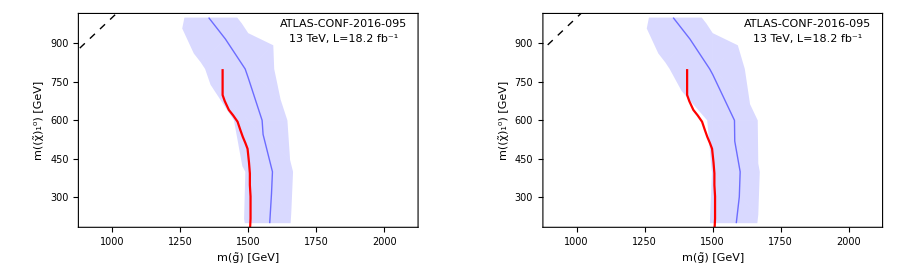

```mathematica
GraphicsRow[{makePlot[searches[[#1]],#2]&@@{9,1},makePlotobs[searches[[#1]],#2]&@@{9,1}},ImageSize->900]
```

```mathematica
GraphicsRow[{makePlot[searches[[#1]],#2]&@@{9,2},makePlotobs[searches[[#1]],#2]&@@{9,2}},ImageSize->900]
```

-Graphics-

-Graphics-

```mathematica
makePlot[searches[[#1]],#2]&@@{9,2}
```

-Graphics-

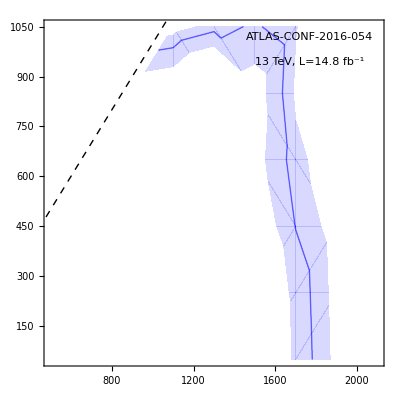

```mathematica
makeExclusionsPlot[searches[[1]],1]
```

### Best Expected plots

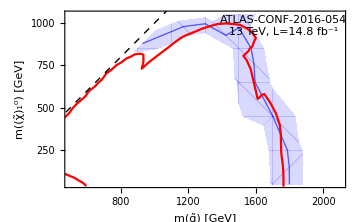
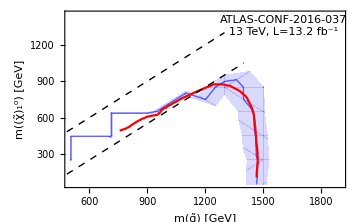
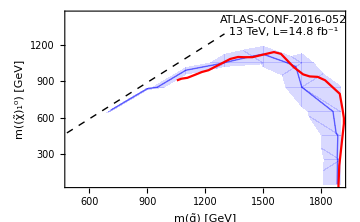
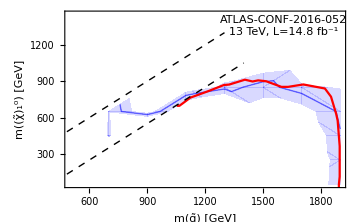
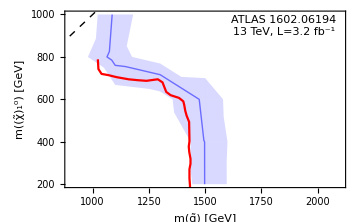
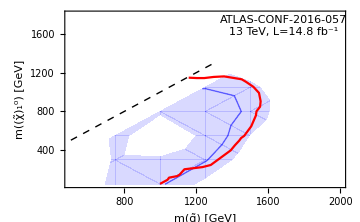
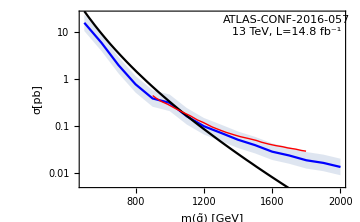
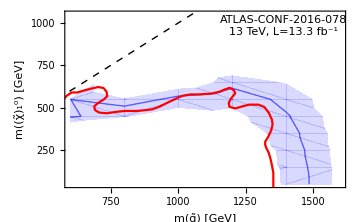
ATLAS_1lepton_j_MET | {-Graphics-}
ATLAS_ss_leptons | {-Graphics-}
ATLAS_multib | {-Graphics-,-Graphics-}
ATLAS_7_10_jet_3fb | {-Graphics-,-Graphics-}
ATLAS_RPV | {-Graphics-,-Graphics-}
ATLAS_CONF2016078_2_6j | {-Graphics-,-Graphics-,-Graphics-}
CMS_jets | {-Graphics-,-Graphics-,-Graphics-,-Graphics-}
ATLAS_lepton_multijet | {-Graphics-}
ATLAS_8_10_jet | {-Graphics-,-Graphics-}

```mathematica
Grid[Table[{search,makePlot[search,#,ImageSize-> Medium]&/@Range[1,Length[validgrids[search]]]},{search,searches}]]
```

#### Save all plots at once

```mathematica
{#,validgrids[#]}&/@searches
```

{{ATLAS_1lepton_j_MET,{M3_C1_N1_results_fat_stable_lepton_results}},{ATLAS_ss_leptons,{M3_tt_M1_results_fat_stable_lepton_results}},{ATLAS_multib,{M3_bb_M1_results_fat_stable_lepton_results,M3_tt_M1_results_fat_stable_lepton_results}},{ATLAS_7_10_jet_3fb,{M3_mu_M1_results_fat_stable_lepton_results}},{ATLAS_RPV,{M3_M1_results_fat_stable_lepton_results,M3_line_results_RPV_fat_lepton_results}},{ATLAS_CONF2016078_2_6j,{sq_M1_results_fat_stable_lepton_results,M3_M1_results_fat_stable_lepton_results,M3_C1_N1_results_fat_stable_lepton_results}},{CMS_jets,{sq_M1_results_fat_stable_lepton_results,M3_tt_M1_results_fat_stable_lepton_results,M3_bb_M1_results_fat_stable_lepton_results,M3_M1_results_fat_stable_lepton_results}},{ATLAS_lepton_multijet,{M3_tt_M1_results_RPV_fat_lepton_results}},{ATLAS_8_10_jet,{M3_mu_M1_results_fat_stable_lepton_results}}}

```mathematica
{{"ATLAS_1lepton_j_MET",{"M3_C1_N1_results_fat_stable_lepton_results"}},{"ATLAS_ss_leptons",{"M3_tt_M1_results_fat_stable_lepton_results"}},{"ATLAS_multib",{"M3_bb_M1_results_fat_stable_lepton_results","M3_tt_M1_results_fat_stable_lepton_results"}},{"ATLAS_7_10_jet_3fb",{"M3_mu_M1_results_fat_stable_lepton_results"}},{"ATLAS_RPV",{"M3_M1_results_fat_stable_lepton_results","M3_line_results_RPV_fat_lepton_results"}},{"ATLAS_CONF2016078_2_6j",{"sq_M1_results_fat_stable_lepton_results","M3_M1_results_fat_stable_lepton_results","M3_C1_N1_results_fat_stable_lepton_results"}},{"CMS_jets",{"sq_M1_results_fat_stable_lepton_results","M3_tt_M1_results_fat_stable_lepton_results","M3_bb_M1_results_fat_stable_lepton_results","M3_M1_results_fat_stable_lepton_results"}},{"ATLAS_lepton_multijet",{"M3_tt_M1_results_fat_stable_lepton_results"}},{"ATLAS_8_10_jet",{"M3_mu_M1_results_fat_stable_lepton_results"}}}
```

```mathematica
For[ss=1,ss≤ Length[searches],ss++,
For[vv=1,vv≤ Length[validgrids[searches[[ss]]]],vv++,
plot[searches[[ss]],vv]=makePlot[searches[[ss]],vv];
Export[searches[[ss]]<>"_"<>validgrids[searches[[ss]]][[vv]]<>".slim_exp.pdf",plot[searches[[ss]],vv]]
]]
```

Re-make additional plots for particular ones that came out not nice-looking

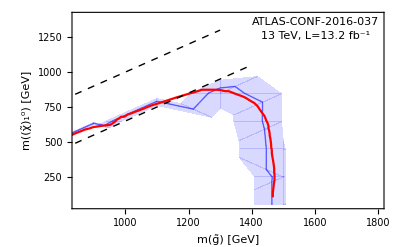

```mathematica
makePlot[searches[[#1]],#2,PlotRange-> {{850,1800},{50,1400}}]&@@(point={2,1})
```

```mathematica
makePlot[searches[[#1]],#2,PlotRange-> {{850,1800},{50,1400}}]&@@(point={3,1})
```

```mathematica
makePlot[searches[[#1]],#2,PlotRange-> {{850,1800},{50,1400}}]&@@(point={3,2})
```

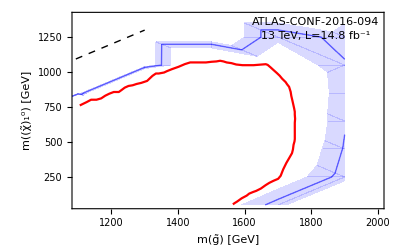

```mathematica
makePlot[searches[[#1]],#2,PlotRange-> {{1100,2000},{50,1400}}]&@@(point={8,1})
```

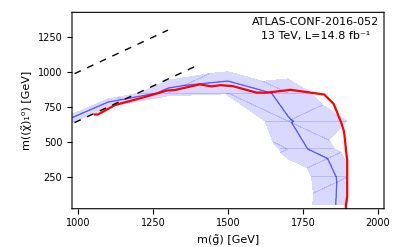

```mathematica
makePlot[searches[[#1]],#2,PlotRange-> {{1000,2000},{50,1400}}]&@@(point={3,2})
```

```mathematica
Export[searches[[#1]]<>"_"<>validgrids[searches[[#1]]][[#2]]<>".slim_exp.pdf",%]&@@point
```

ATLAS_multib_M3_tt_M1_results_fat_stable_lepton_results.slim.pdf

### Best Observed plots

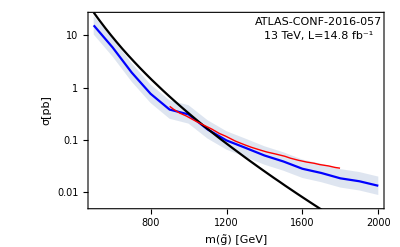

```mathematica
makePlotobs[searches[[#1]],#2]&@@{5,2}
```

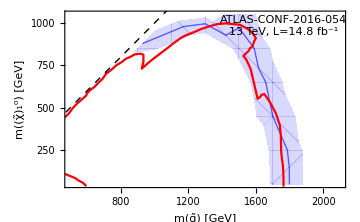
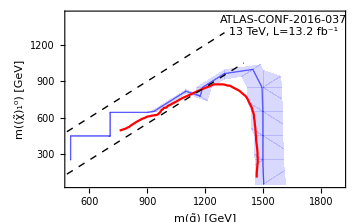
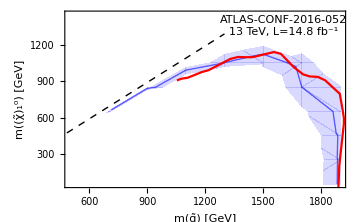
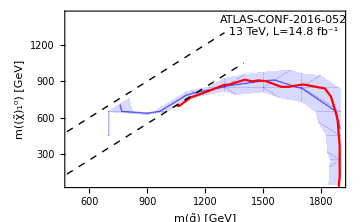
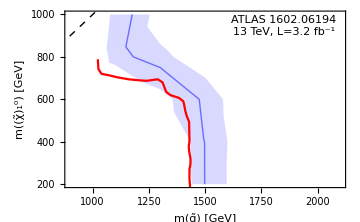
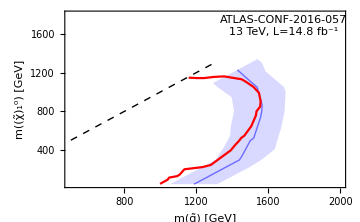
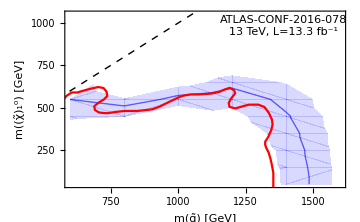
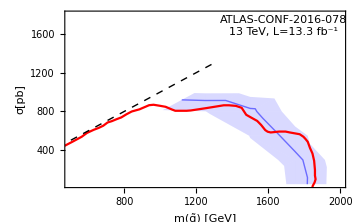
ATLAS_1lepton_j_MET | {-Graphics-}
ATLAS_ss_leptons | {-Graphics-}
ATLAS_multib | {-Graphics-,-Graphics-}
ATLAS_7_10_jet_3fb | {-Graphics-,-Graphics-}
ATLAS_RPV | {-Graphics-,-Graphics-}
ATLAS_CONF2016078_2_6j | {-Graphics-,-Graphics-,-Graphics-}
CMS_jets | {-Graphics-,-Graphics-,-Graphics-,-Graphics-}
ATLAS_lepton_multijet | {-Graphics-}
ATLAS_8_10_jet | {-Graphics-,-Graphics-}

```mathematica
Grid[Table[{search,makePlotobs[search,#,ImageSize-> Medium]&/@Range[1,Length[validgrids[search]]]},{search,searches}]]
```

```mathematica
For[ss=1,ss≤ Length[searches],ss++,
For[vv=1,vv≤ Length[validgrids[searches[[ss]]]],vv++,
plot[searches[[ss]],vv]=makePlotobs[searches[[ss]],vv];
Export[searches[[ss]]<>"_"<>validgrids[searches[[ss]]][[vv]]<>".slim_obs.pdf",plot[searches[[ss]],vv]]
]]
```